```mathematica
ClearAll["Global`*"];
```

## Memory from BOB model

```mathematica
(*Computing the final spin of the blackholes*)
p0 = 0.04826; p1=0.01559; p2 = 0.00485; s4 = -0.1229; s5 = 0.4537; t0 = -2.8904; t2 = -3.5171; t3 = 2.5763; q=1; eta = 1/4; theta = π/2; 
pct= 0.99; tcut = 200; tmin = -20; tmax = 50;
```

```mathematica
Mf[α1_, α2_]:= 1- p0 - p1 (α1+ α2) - p2(α1+ α2)^2
αb[α1_, α2_]:= (q^2 α1+ α2)/(q^2+1)
```

```mathematica
Alpha[α1_, α2_]:= αb[α1, α2] + s4 eta  αb[α1, α2]^2 + s5 eta^2 αb[α1, α2]  + t0 eta αb[α1, α2]  + 2 √3 eta +  t2 eta^2 + t3 eta^3
```

```mathematica
(*ISCO calcualtion*)
Z1[af_]:= 1 + (1-af^2)^(1/3)((1+af)^(1/3) + (1-af)^(1/3))
Z2[af_, Z1_]:= √(3 af^2 + Z1^2)
RISCO[Z1_, Z2_]:= 3 + Z2 - √((3-Z1)(3+ Z1 + 2 Z2))
OMISCO[RISCO_, af_]:= 1/(RISCO^(3/2)+ af )
OMQNM[α1_, α2_]:= (1- 0.63 (1-αb[α1, α2])^0.3)/(2Mf[α1, α2])
```

```mathematica
(*BOB memory calculation*)
Y20[θ_]:=1/4 √(15/(2 π))Sin[θ]^2
Q[af_] := 2 (1-af)^-0.45
```

```mathematica
TAO[α1_, α2_]:= 2 Q[αb[α1, α2]]Mf[α1, α2]/(1- 0.63 (1-αb[α1, α2])^0.3)
```

```mathematica
Ap[α1_, α2_] := 1.068(1-Mf[α1, α2])^0.8918
OMREF[α1_, α2_]:= OMISCO[RISCO[Z1[αb[α1, α2]], Z2[αb[α1, α2], Z1[αb[α1, α2]]]], αb[α1, α2]]
```

```mathematica
OMP[α1_, α2_]:= ((OMQNM[α1, α2]^4 + OMREF[α1, α2]^4)/2)^(1/4)
OMM[α1_, α2_]:= ((OMQNM[α1, α2]^4 - OMREF[α1, α2]^4)/2)^(1/4)
```

```mathematica
(*Slight consusion over sign*)
KAPPAM[α1_, α2_]:= ((OMP[α1, α2]^4 + OMM[α1, α2]^4))^(1/4)
KAPPAP[α1_, α2_]:= ((OMP[α1, α2]^4 - OMM[α1, α2]^4))^(1/4)
(*BOB Memory*)
OM[t_, α1_, α2_]:= (OMP[α1, α2]^4 + OMM[α1, α2]^4 Tanh[t/TAO[α1, α2]])^(1/4)
```

```mathematica
MEMBOB[t_, α1_, α2_]:= (Sin[theta]^2)(17 + (Cos[theta])^2)Ap[α1, α2]^2 TAO[α1, α2]OM[t, α1, α2]^2/OMM[α1, α2]^4
```

```mathematica
BOBmemScale[scale_]:= Plot[MEMBOB[t, scale, scale]-MEMBOB[-500, scale, scale], {t, -100, 50}, PlotRange->{{-100, 50},{-10.0, 45.0}}]
```

```mathematica
Manipulate[BOBmemScale[n], {n, -0.9, 0.9}]
```

```mathematica
BOBmemScale2[scale1_, scale2_]:= Plot[MEMBOB[t, scale1, scale2]-MEMBOB[-500, scale1, scale2], {t, -100, 50}, PlotRange->{{-100, 50},{-10.0, 45.0}}]
```

```mathematica
Manipulate[BOBmemScale2[a, b], {a, -0.9, 0.9}, {b, -0.9, 0.9}]
```

```mathematica
Eqn[α1_, α2_]:= NDSolve[{h'[t]==MEMBOB[t, α1, α2]-MEMBOB[-500, α1, α2], h[0]==0},h, {t, -60,40}]
```

```mathematica
Inthmem[scale_] := Plot[{Evaluate[h[t]/.Eqn[scale,scale]]}, {t,-40,40}, PlotRange->{{-40, 40},{-400.0, 1500.0}}]
```

```mathematica
Manipulate[Inthmem[n] , {n, -0.9, 0.9}]
```

```mathematica
Res[t_, α1_, α2_] :=h[t] /. Eqn[α1, α2]
```

```mathematica
generateBOBmemdata[α1_, α2_, ti_, tf_, dt_]:=Res[#, α1, α2]& /@ Range[ti, tf, dt]
```

```mathematica
dataBoBmem[α1_, α2_, ti_, tf_, dt_] :=Transpose@{Range[ti, tf, dt], generateBOBmemdata[ α1, α2, ti, tf, dt][[All, 1]]}
```

```mathematica
parabolaBoBmem[ t_, α1_, α2_, ti_, tf_, dt_]:=Fit[dataBoBmem[α1, α2, ti, tf, dt],{1,x,x^2},x]/.x-> t;
```

```mathematica
ResMquad[t_, α1_, α2_, ti_, tf_, dt_] := Res[t, α1, α2] - parabolaBoBmem[t, α1, α2, ti, tf, dt]
```

```mathematica
ResFinal[ α1_, α2_, ti_, tf_, dt_] :=Part[ResMquad[#, α1, α2, ti, tf, dt]& /@ Range[ti, tf, dt],  All, 1]
```

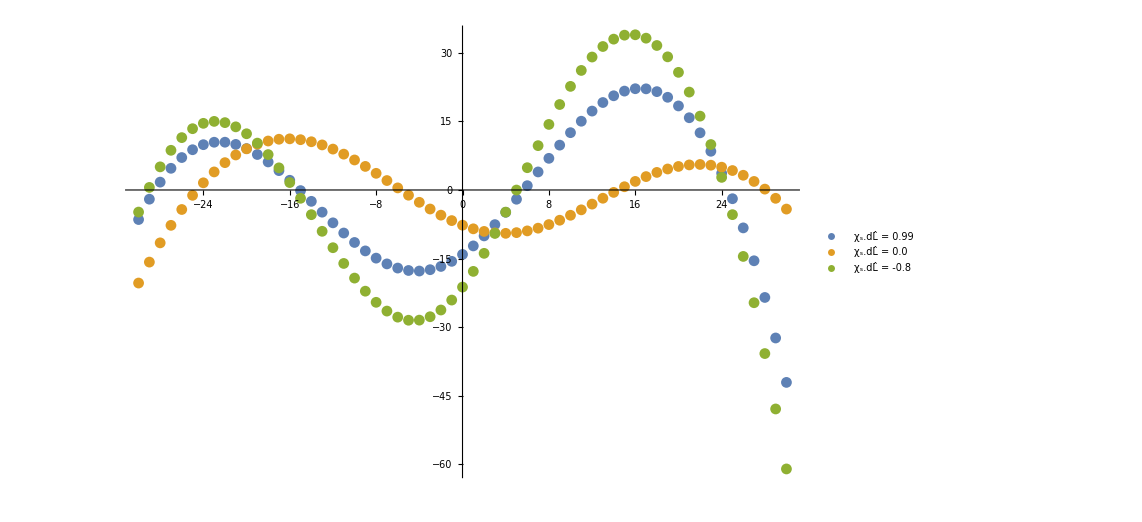

```mathematica
ListPlot[{Transpose@{Range[-30, 30, 1],ResFinal[ 0.9, 0.9, -30, 30,1 ]},  Transpose@{Range[-30, 30, 1],ResFinal[ -0.8,-0.8, -30, 30, 1 ]},  Transpose@{Range[-30, 30, 1],ResFinal[ 0,0, -30, 30, 1 ]}},PlotLegends->Placed[{"χ_s.dL̂ = 0.99", "χ_s.dL̂ = 0.0","χ_s.dL̂ = -0.8"},{0.120,0.87}]]
```

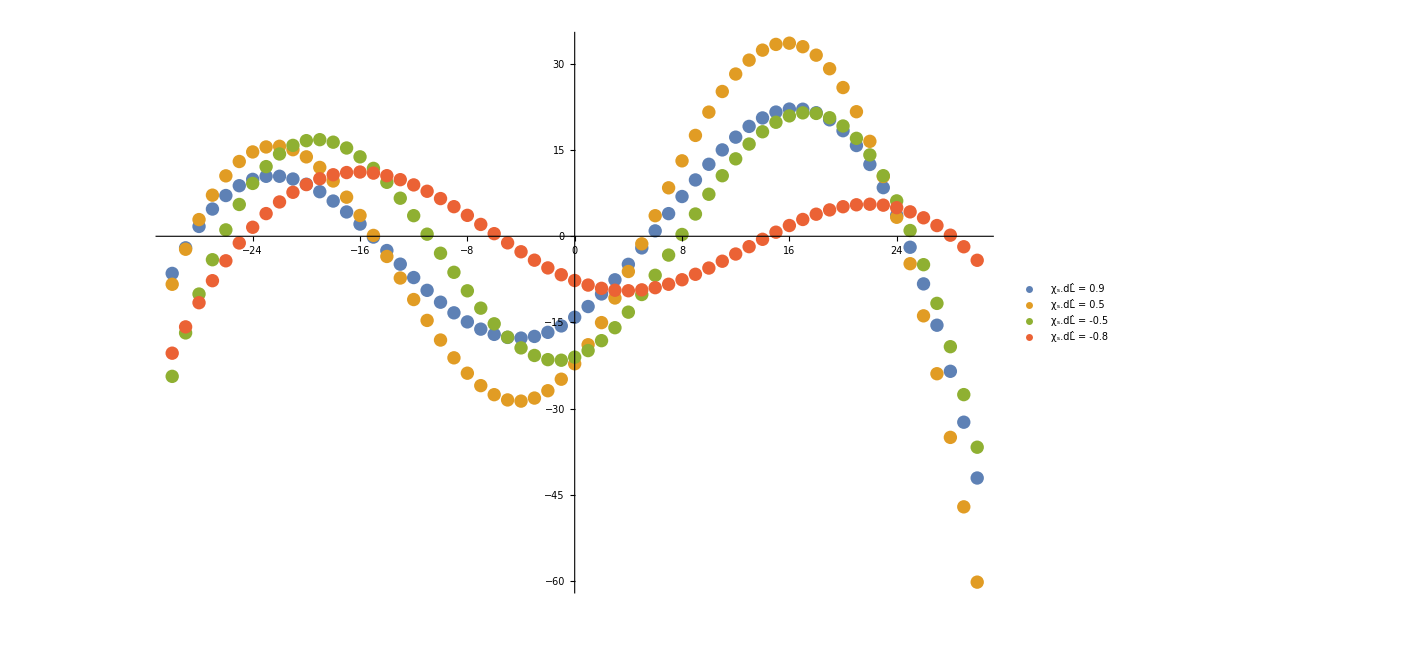

```mathematica
ListPlot[{Transpose@{Range[-30, 30, 1],ResFinal[ 0.9, 0.9, -30, 30,1 ]},  Transpose@{Range[-30, 30, 1],ResFinal[ 0.5,0.5, -30, 30, 1 ]},  Transpose@{Range[-30, 30, 1],ResFinal[ -0.5,-0.5, -30, 30, 1 ]},Transpose@{Range[-30, 30, 1],ResFinal[ -0.8,-0.8, -30, 30, 1 ]}},PlotLegends->Placed[{"χ_s.dL̂ = 0.9", "χ_s.dL̂ = 0.5","χ_s.dL̂ = -0.5", "χ_s.dL̂ = -0.8"},{0.120,0.9}]]
```

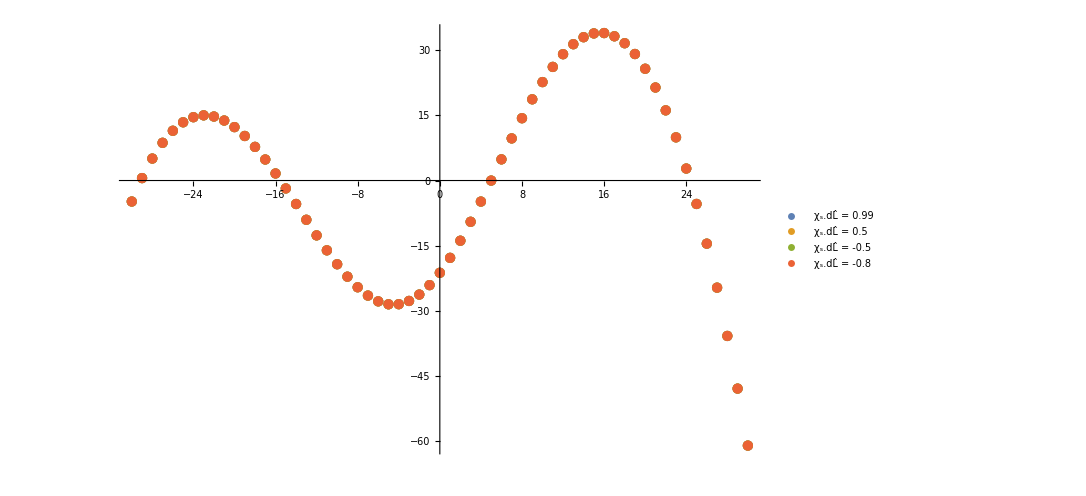

```mathematica
ListPlot[{Transpose@{Range[-30, 30, 1],ResFinal[ 0.99, -0.99, -30, 30,1 ]},  Transpose@{Range[-30, 30, 1],ResFinal[ 0.5,-0.5, -30, 30, 1 ]},  Transpose@{Range[-30, 30, 1],ResFinal[ -0.5,0.5, -30, 30, 1 ]},Transpose@{Range[-30, 30, 1],ResFinal[ -0.8,0.8, -30, 30, 1 ]}},PlotLegends->Placed[{"χ_s.dL̂ = 0.99", "χ_s.dL̂ = 0.5","χ_s.dL̂ = -0.5", "χ_s.dL̂ = -0.8"},{0.120,0.9}]]
```